```mathematica
(*Erlang Distribution*)
```

```mathematica
cdferlang[x_]:=1-Sum[1/n! Exp[-k*σ*x]*(k*σ*x)^n, {n, 0, k-1}]
```

```mathematica
FindRoot[{cdferlang[13.0]==9/10, cdferlang[8.2]==1/10}, {{k, 3},{σ, 1/11.5}}]
```

{k→31.3044,σ→0.0949845}

```mathematica
Solve[cdferlang[10.2]==1/2, {σ}, Reals] /. k->31
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{σ→0.0969871}}

```mathematica
pdferlang[x_]:=(k σ)^k x^(k-1) Exp[-(k σ x)]/(k-1)!
```

```mathematica
k :=31
σ := 0.09698706953718507
```

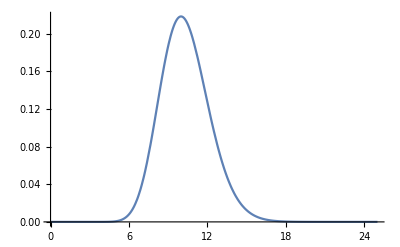

```mathematica
Plot[pdferlang[x], {x, 0, 25}]
```